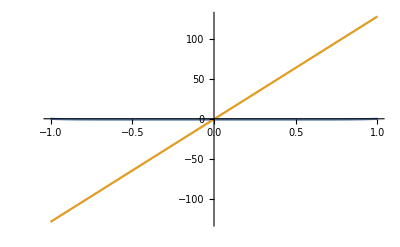

-43.3043

```mathematica
theta=Pi/2.01;
d=-.5;
y1 =-.;
y2 =0;
y3=.9731;
hullFunc = y^10-1;
waterFunc = Tan[theta]*y+d;
Plot[{hullFunc,waterFunc},{y,-1,1}]
case1=N[Integrate[1,{y,y1,y3},{z,hullFunc,waterFunc}]];
case2=Integrate[1,{y,y1,y2},{z,hullFunc,waterFunc}]+Integrate[1,{y,y2,1},{z,hullFunc,0}]
```